```mathematica
s=NDSolve[{
S'[t]==-0.5*S[t]*Z[t]+0.01*S[t]*(1-S[t]/500),
Z'[t]==(0.5-0.6)*S[t]*Z[t]+0.1*R[t],
R'[t]==0.6*S[t]*Z[t]-0.1*R[t],
S[0]==499,Z[0]==1,R[0]==0},{S,Z,R},{t,0,1000}]
```

{{S→InterpolatingFunction[…],Z→InterpolatingFunction[…],R→InterpolatingFunction[…]}}

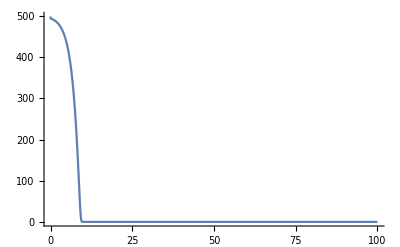

```mathematica
Plot[Evaluate[S[t]/.s],{t,0,100},PlotRange->All]
```

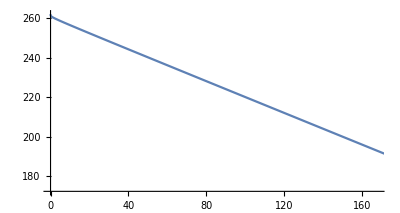

```mathematica
ParametricPlot[Evaluate[{S[t],Z[t]}/.s],{t,0,0.1}]
```